# Benefits of marriage as a search strategy

by Davi B. Costa

We propose and investigate a model for dating and marriage in large societies based on a stochastic matching process and simple decision rules. Agents have preferences among themselves given by some probability distribution. They randomly search for better mates, forming new couples and breaking apart in the process. Marriage is implemented in the model by adding the decision of stopping searching for a better mate when an agent finds another one with an affinity higher than a certain fixed amount. We show that the average utility in the system with marriage can be higher than in the system without it. Part of our results can be summarized in what sounds like a piece of advice: don’t marry the first person you like and don’t search for the love of your life, but get married if you like your partner more than a sigma above average. We also compare the evolution of the fraction of married couples in our model with real data and obtain good agreement. In the last section, we formulate the model in the limit of an infinite number of agents and find an analytical expression for the evolution of the system.

(This Mathematica notebook is a companion to the article: https://arxiv.org/abs/2108.04885. More details can be found in the article which is freely available in the Arxiv repository)

## 1. Introduction

Consider the following situation: you are dating and wonder whether you should propose marriage or not. There are many aspects of marriage to consider, but you are mainly concerned with marriage as a search strategy. You like your mate, but you are unsure if it is enough. After all, there may be someone out there that you would like even more, but it is unlikely that you will get to know this person if you get married. Perhaps, the best is to stay open to the possibility of meeting a potential better mate by not getting married. However, if your relationship is symmetric in this respect, you may become single because your mate left you for someone else. So while marriage closes off some of the opportunities that you would otherwise have, on the other hand, it protects you from the risk of being left out. So you ask yourself: as a search strategy, is it beneficial to get married? Or does the potential benefit of meeting a person with whom you have a greater affinity outweigh the chances of being alone because your current partner has left you? To make these ideas precise and to answer the
question, we propose a model for dating and marriage based on a random matching process and simple decision rules.

The model contains a number N of agents with preferences among themselves sampled by a given distribution. Initially, all agents are singles, and the system evolves in a certain number T of discrete steps. At each step, they will match in pairs by random chance. If the agents of the matched pair like each other more than their previous mates, or more than being single, they will form a new couple. An agent becomes single if its partner starts a new relationship. Marriage is implemented in the model by adding the decision of stopping searching for a better mate when an agent finds another one with an affinity higher than a certain fixed value Λ. This parameter should be interpreted as exogenous in the sense that it characterizes the decision behavior of the agents of a given society with respect to marriage. We simulate this system for different values of Λ and we computed the average utility in each case as a function of the number of steps. Part of the conclusions one can extract from the results we obtained, answers the question from the previous paragraph. The answer sounds like a piece of advice: don’t marry the first person you like and don’t search for the love of your life, but get married if you like your partner more than a sigma above average.

## 2. Model and results

### 2.1. The model

The model contains n agents with preferences among themselves described by a utility function. This information is encoded in the off-diagonal elements of the affinity matrix A∈ℝ^(n x n), where A_ij is the utility for agent i to be in a couple with agent j. In large societies, the probability distribution that generates the affinity matrix is more important than its actual values. Indeed, the preferences of agent k concerning the other agents of society are encoded by {A_kj:1≤j≤n & j≠k} . The histogram with these values, will distribute according to some probability distribution. As it happens with many human traits, it may be reasonable to assume that these values are generated by a Gaussian distribution, i.e., A_kj∼N(μ_k,σ_k) for all 1≤j≤n with j≠k and each 1≤k≤n. In principle, one may think that it is more realistic to assume that the preferences of different agents are given by distributions defined with different parameters μ and σ. Note, however, that the values of the k-column of the affinity matrix, {A_jk:1≤j≤n & j≠k} , encodes the way agent k is liked by society. Therefore, if agents indeed have preferences given by different Gaussian distributions, then the distribution that generates the columns of the affinity matrix will not in general be Gaussian. Hence, to have both lines and columns consistently Gaussian, we may assume that all off-diagonal entries of the affinity matrix are generated by the same Gaussian distribution, that is,  A_kj∼N(μ,σ) for all 1≤j≤n and 1≤k≤n with j≤k. When this is the case, we will say that we are dealing with the Gaussian model. For comparison and to make concrete our analytical investigations, we will also study the Uniform model, i.e., A_kj∼U(μ-2σ,μ+2σ) .
	The diagonal elements of the affinity matrix are the utilities when agents are singles. We also believe it is reasonable to assume these values are generated by a Gaussian distribution A_kk∼N(μ_s,σ_s) for all  1≤k≤n. It is an open empirical problem to investigate the relation between the distributions that generate the diagonal and off-diagonal elements of the affinity matrix. In particular, it would be interesting to investigate the relationship between the mean of these distributions. Note, that the mean of the diagonal elements gives the average utility when all agents are single. On the other hand, the mean of the off-diagonal elements can be interpreted as the average utility when agents form random couples. Therefore, the relationship between the mean of these two distributions encodes how being single compares to dating a random agent in society. We denote the mean and variance of this distribution using an s.
	In Wolfram Language we can generate the affinity matrix for the Gaussian model with parameters:

```mathematica
{n=1000,μ=0,σ=1,μs=0,σs=1};
```

using

```mathematica
A=RandomVariate[NormalDistribution[μ,σ],{n,n}]; 
Do[A⟦k⟧⟦k⟧=RandomVariate[NormalDistribution[μs,σs],1]⟦1⟧,{k,1,n}];
```

Initially, all agents are singles, therefore their initial utilities (u^k)_twill be given by the diagonal elements of the affinity matrix, i.e.,

```mathematica
Couples={{}};
Utility={Table[A⟦k⟧⟦k⟧,{k,1,n}]};
```

The histogram with this values follows a Gaussian distribution and can be visualized easily using:

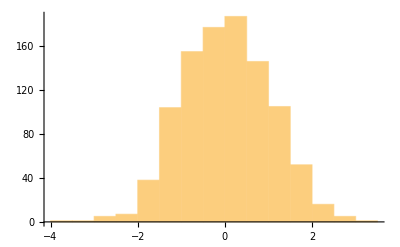

```mathematica
Histogram[Table[A⟦k⟧⟦k⟧,{k,1,n}]]
```

The dynamics of the system happen in discrete steps t∈Ν. At each step t, all agents match at random with a new agent. In Wolfram language, the matching at each step can be generated easily using

```mathematica
var=RandomSample[Table[k,{k,1,n}]];
Matching={var⟦1;;n/2⟧,var⟦n/2+1;;n⟧}ᵀ;
Matching⟦1;;100⟧
```

{{976,569},{532,77},{691,274},{956,372},{60,538},{397,719},{905,108},{775,812},{334,54},{336,255},{162,579},{110,379},{444,600},{156,295},{59,92},{96,196},{131,542},{854,925},{643,957},{584,988},{455,550},{892,891},{181,283},{615,159},{866,163},{392,248},{486,776},{19,598},{498,610},{128,785},{992,818},{402,961},{589,895},{256,217},{906,411},{605,55},{636,575},{186,56},{754,889},{31,183},{138,699},{506,377},{24,595},{800,844},{198,212},{480,266},{609,350},{872,603},{259,384},{133,676},{134,306},{487,788},{435,69},{722,199},{644,469},{164,141},{771,170},{739,479},{790,684},{508,543},{187,545},{105,244},{179,705},{80,637},{929,180},{793,554},{355,525},{824,953},{356,1000},{120,693},{75,549},{102,341},{453,305},{201,149},{933,831},{171,884},{580,747},{727,61},{429,316},{802,529},{916,917},{852,870},{984,968},{252,382},{910,416},{618,299},{690,191},{33,482},{839,39},{227,275},{808,330},{899,519},{819,945},{749,222},{991,143},{136,323},{978,368},{582,119},{806,66},{874,623}}

We see that each element of the Matching is a pair of numbers {j,k} denoting the agents that match at the given step. 
Then, two agents that were matched at step t+1 will form a couple if they like themselves. That is, if their their affinities are higher then their utilities at t. More precisely:

```mathematica
t=1;
Match=Table[{a,b}=Matching⟦i⟧;A⟦a,b⟧>Utility⟦t⟧⟦a⟧&&A⟦b,a⟧>Utility⟦t⟧⟦b⟧,{i,1,Length[Matching]}];
NewCouples=Pick[Matching,Match]
```

{{976,569},{691,274},{162,579},{131,542},{584,988},{19,598},{992,818},{589,895},{186,56},{754,889},{198,212},{609,350},{487,788},{164,141},{793,554},{429,316},{852,870},{910,416},{899,519},{749,222},{806,66},{546,697},{125,279},{369,267},{151,879},{888,616},{608,718},{548,90},{594,652},{428,418},{655,563},{886,93},{380,611},{726,666},{385,296},{137,770},{314,841},{781,439},{124,779},{552,920},{887,247},{900,566},{787,348},{219,977},{253,972},{515,2},{358,875},{958,271},{537,881},{997,11},{474,667},{346,441},{381,203},{680,646},{583,494},{261,663},{78,322},{361,329},{633,914},{47,896},{438,68},{189,626},{311,41},{915,404},{570,386},{650,437},{970,70},{642,522},{512,202},{139,581},{446,224},{702,22},{485,333},{942,707},{835,863},{106,332},{176,25},{412,484},{197,943},{194,43},{127,908},{632,339},{757,122},{833,351},{574,533},{338,123},{406,476},{557,36},{81,620},{733,284},{270,963},{838,924},{432,617},{396,540},{712,282},{948,209},{390,999},{445,98},{154,867},{941,62},{661,157},{461,568},{856,560},{743,918},{671,829},{413,679},{99,234},{460,729},{114,496},{994,465},{32,682},{648,319},{599,504},{292,966},{974,257},{12,764}}

If one of the agents of the new couple was dating before, it will break apart with its previous mate:

```mathematica
BreakingAgents= Select[Flatten[NewCouples],MemberQ[Flatten[Couples⟦t⟧],#]&];
CouplesToBreak = Select[Couples⟦t⟧, MemberQ[BreakingAgents,#⟦1⟧] || MemberQ[BreakingAgents, #⟦2⟧] &];
```

Then, the couples at t+1 will be the set of Couples at t, plus the set of NewCouples, minus the CouplesToBreak:

```mathematica
Couples=Join[Couples,{Join[Complement[Couples⟦t⟧,CouplesToBreak],NewCouples]}];
Couples⟦t+1⟧
```

{{976,569},{691,274},{162,579},{131,542},{584,988},{19,598},{992,818},{589,895},{186,56},{754,889},{198,212},{609,350},{487,788},{164,141},{793,554},{429,316},{852,870},{910,416},{899,519},{749,222},{806,66},{546,697},{125,279},{369,267},{151,879},{888,616},{608,718},{548,90},{594,652},{428,418},{655,563},{886,93},{380,611},{726,666},{385,296},{137,770},{314,841},{781,439},{124,779},{552,920},{887,247},{900,566},{787,348},{219,977},{253,972},{515,2},{358,875},{958,271},{537,881},{997,11},{474,667},{346,441},{381,203},{680,646},{583,494},{261,663},{78,322},{361,329},{633,914},{47,896},{438,68},{189,626},{311,41},{915,404},{570,386},{650,437},{970,70},{642,522},{512,202},{139,581},{446,224},{702,22},{485,333},{942,707},{835,863},{106,332},{176,25},{412,484},{197,943},{194,43},{127,908},{632,339},{757,122},{833,351},{574,533},{338,123},{406,476},{557,36},{81,620},{733,284},{270,963},{838,924},{432,617},{396,540},{712,282},{948,209},{390,999},{445,98},{154,867},{941,62},{661,157},{461,568},{856,560},{743,918},{671,829},{413,679},{99,234},{460,729},{114,496},{994,465},{32,682},{648,319},{599,504},{292,966},{974,257},{12,764}}

Now, the utilities will be updated using the affinities of the couples:

```mathematica
NewUtility=Utility⟦1⟧; 
Do[
{a,b}=Couples⟦t+1⟧⟦k⟧;
NewUtility⟦a⟧=A⟦a,b⟧;
NewUtility⟦b⟧=A⟦b,a⟧,
{k,1,Length[Couples⟦t+1⟧]}];
Utility=Join[Utility,{NewUtility}];
```

Note that the initial average utility is approximate equal to μ=0,

```mathematica
Mean[Utility⟦1⟧]
```

0.0389645

However, the average utility at t=1 is higher seems many agents started a relationship:

```mathematica
Mean[Utility⟦2⟧]
```

0.297775

Applying these simple decision rules and using this stochastic matching process we can evolve the system a number T  of steps. Before doing this, let’s show our implementation of marriage.
If the affinity between a couple is higher than a certain fixed value Λ∈ℝ, then the couple will not match with new agents in the next steps of the evolution.	The difference in the implementation is that now, after getting Couples we will also construct the Married couples. For Λ=1 we would add

```mathematica
Λ=1;
Married=Select[Couples⟦t+1⟧,A⟦#⟦1⟧⟧⟦#⟦2⟧⟧>Λ&&A⟦#⟦2⟧⟧⟦#⟦1⟧⟧>Λ&]
```

{{976,569},{162,579},{19,598},{164,141},{888,616},{594,652},{428,418},{633,914},{189,626},{915,404},{512,202},{270,963},{941,62},{32,682}}

Then, in the next step t+2, the Married couples would not participate in the matching process. We can do this using

```mathematica
varΛ=RandomSample[Complement[Table[k,{k,1,n}],Flatten[Married]]];MatchingΛ={varΛ⟦1;;Length[varΛ]/2⟧,varΛ⟦Length[varΛ]/2+1;;Length[varΛ]⟧}ᵀ;
```

instead of “var” and “Matching” as we used before.

We collected all these material and constructed the DatingMarriageModel function. Schematically we have:

DatingMarriageModel[dist_,n_,μ_,σ_,μs_,σs_,Λ_,T_] →{A,Utility,UtilityΛ,Couples,CouplesΛ,Married}
​
Input:
dist=Distribution used in the simulation, either “U”=Uniform or “N”=Normal/Gaussian;
n = Number of agents;
μ,σ = Mean and variance of the distribution that generates the off-diagonal elements of the affinity matrix;
μs,σs = Mean and variance of the distribution that generates the diagonal elements of the affinity matrix;
Λ = Parameter that defines marriage;
T = Number of steps of the simulaton.
​
Output:
A = Affinity matrix N x N;
Utility = Utility matrix U x T, where u⟦t⟧⟦k⟧ is the utility of agent k at step t in the system without marriage;
UtilityΛ = Utility matrix U x T, where u⟦t⟧⟦k⟧ is the utility of agent k at step t in the system with marriage;
Couples = List of length T, with Couples⟦t⟧ the set of couples at step t in the system without marriage;
CouplesΛ = List of length T, with Couples⟦t⟧ the set of couples at step t in the system with marriage;
Married=List of all agents who get married. Combined with CouplesΛ one can create a list with agents married at each step t.

```mathematica
DatingMarriageModel[dist_,n_,μ_,σ_,μs_,σs_,Λ_,T_]:=
Module[{A,Utility,UtilityΛ,Couples,CouplesΛ,Married,t,var,varΛ,Matching,MatchingΛ,a,b,Love,LoveΛ,NewCouples,NewCouplesΛ,Infidels,InfidelsΛ,CouplesToBreak,CouplesToBreakΛ,NewUtility,NewUtilityΛ,k},


If[dist=="N",
A=RandomVariate[NormalDistribution[μ,σ],{n,n}]; 
Do[A⟦k⟧⟦k⟧=RandomVariate[NormalDistribution[μs,σs],1]⟦1⟧,{k,1,n}]];

If[dist=="U",
A=RandomVariate[UniformDistribution[{μ-2σ,μ+2σ}],{n,n}]; 
Do[A⟦k⟧⟦k⟧=RandomVariate[UniformDistribution[{μs-2σs,μs+2σs}],1]⟦1⟧,{k,1,n}] ];
(*A is the affinity matrix. Subscript[A, kj] is the utility surplus for agent k when it is with agent j; Subscript[A, kk] is the utility for agent k when it is single.*) 

Utility={Table[A⟦k⟧⟦k⟧,{k,1,n}]}; 
UtilityΛ={Table[A⟦k⟧⟦k⟧,{k,1,n}]}; 

(*Creates a list with the initial utilities in the system with marriage and in the system without marriage which is Subscript[A, kk] seems all agents are singles initially. We are using Λ to denote the attributes of the system with marriage*)

Couples={{}};
CouplesΛ={{}};
Married={};

Do[
t=Length[Utility];

(*Without marriage*)

var=RandomSample[Table[k,{k,1,n}]];
Matching={var⟦1;;n/2⟧,var⟦n/2+1;;n⟧}ᵀ;(*Random matching between agents*)

Love=Table[
{a,b}=Matching⟦i⟧;
A⟦a,b⟧>Utility⟦t⟧⟦a⟧&&A⟦b,a⟧>Utility⟦t⟧⟦b⟧,
{i,1,Length[Matching]}]; (*Array with the couples that accept each other*)
NewCouples=Pick[Matching,Love];
Infidels=Select[Flatten[NewCouples],MemberQ[Flatten[Couples⟦t⟧],#]&];
CouplesToBreak=Select[Couples⟦t⟧,MemberQ[Infidels,#⟦1⟧]||MemberQ[Infidels,#⟦2⟧]&];
Couples=Join[Couples,{Join[Complement[Couples⟦t⟧,CouplesToBreak],NewCouples]}];(*Creates a new entry in couples with the couples at the next step. The couples at the next step are the old couples - the couples that broke + the new couples*)

(*Construct the utility in the next step*)
NewUtility=Utility⟦1⟧; 
Do[
{a,b}=Couples⟦t+1⟧⟦k⟧;
NewUtility⟦a⟧=A⟦a,b⟧;
NewUtility⟦b⟧=A⟦b,a⟧,
{k,1,Length[Couples⟦t+1⟧]}];
Utility=Join[Utility,{NewUtility}];


(*With marriage*)
varΛ=RandomSample[Complement[Table[k,{k,1,n}],Flatten[Married]]];MatchingΛ={varΛ⟦1;;Length[varΛ]/2⟧,varΛ⟦Length[varΛ]/2+1;;Length[varΛ]⟧}ᵀ;
LoveΛ=Table[
{a,b}=MatchingΛ⟦i⟧;
A⟦a,b⟧>UtilityΛ⟦t⟧⟦a⟧&&A⟦b,a⟧>UtilityΛ⟦t⟧⟦b⟧&&Not[MemberQ[Flatten[Married],a]]&&Not[MemberQ[Flatten[Married],b]],
{i,1,Length[MatchingΛ]}];
NewCouplesΛ=Pick[MatchingΛ,LoveΛ];
InfidelsΛ=Select[Flatten[NewCouplesΛ],MemberQ[Flatten[CouplesΛ⟦t⟧],#]&];
CouplesToBreakΛ=Select[CouplesΛ⟦t⟧,MemberQ[InfidelsΛ,#⟦1⟧]||MemberQ[InfidelsΛ,#⟦2⟧]&];
CouplesΛ=Join[CouplesΛ,{Join[Complement[CouplesΛ⟦t⟧,CouplesToBreakΛ],NewCouplesΛ]}];
Married=Select[CouplesΛ⟦t+1⟧,A⟦#⟦1⟧⟧⟦#⟦2⟧⟧>Λ&&A⟦#⟦2⟧⟧⟦#⟦1⟧⟧>Λ&];
NewUtilityΛ=UtilityΛ⟦1⟧;
Do[
{a,b}=CouplesΛ⟦t+1⟧⟦k⟧;
NewUtilityΛ⟦a⟧=A⟦a,b⟧;
NewUtilityΛ⟦b⟧=A⟦b,a⟧,
{k,1,Length[CouplesΛ⟦t+1⟧]}];
UtilityΛ=Join[UtilityΛ,{NewUtilityΛ}],
T];
{A,Utility,UtilityΛ,Couples,CouplesΛ,Married}]
```

### 2.2. Results

Now we will present the results obtained in our simulation for the Gaussian model with

```mathematica
{n=1000,μ=0,σ=1,μs=0,σs=1,Λ=1,T=100};
```

First we run our DatingMarriageModel simulation:

```mathematica
r=DatingMarriageModel["N",n,μ,σ,μs,σs,Λ,T];
```

Because we are concerned with large societies, we are more interested in the average utility u_t and its variance than in individual utilities (u^k)_t. The marked difference between (u^k)_t and u_t can be visualized by plotting their values. The utilities of agents 1,2,3 and 4 evolves as:

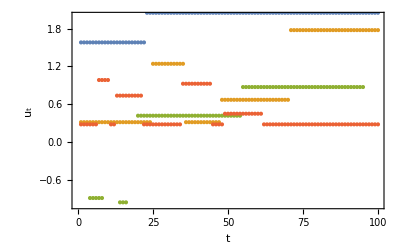

```mathematica
ListPlot[Table[{r⟦2⟧⟦k⟧⟦1⟧,r⟦2⟧⟦k⟧⟦2⟧,r⟦2⟧⟦k⟧⟦3⟧,r⟦2⟧⟦k⟧⟦4⟧},{k,1,T}]ᵀ,IntervalMarkers->"Bands",Frame->True,FrameLabel->{Style["t",14],Style["u_t",14]},PlotRange->{All,{-1,2}}]
```

On the other hand, the average utility u_t together with its variance evolve as:

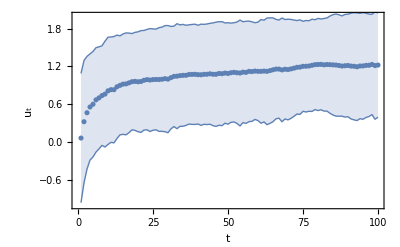

```mathematica
ListPlot[Table[Around[Mean[r⟦2⟧⟦k⟧],Variance[r⟦2⟧⟦k⟧]],{k,1,T}],IntervalMarkers->"Bands",Frame->True,FrameLabel->{Style["t",14],Style["u_t",14]},PlotRange->{All,{-1,2}}]
```

For comparison, we can run the simulation for the Uniform model and plot the evolution of average utility as above

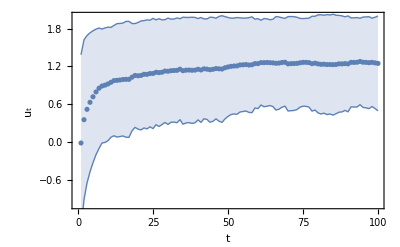

```mathematica
rU=DatingMarriageModel["U",n,μ,σ,μs,σs,Λ,T];
ListPlot[Table[Around[Mean[rU⟦2⟧⟦k⟧],Variance[rU⟦2⟧⟦k⟧]],{k,1,T}],IntervalMarkers->"Bands",Frame->True,FrameLabel->{Style["t",14],Style["u_t",14]},PlotRange->{All,{-1,2}}]
```

We see that both results are very similar. Another quantity of interest is the fraction of couples. We have:

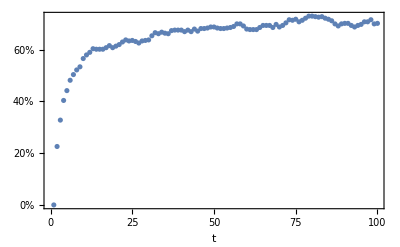

```mathematica
CouplesNumber=Table[Length[r⟦4⟧⟦k⟧],{k,1,T}];
ListPlot[(2{CouplesNumber})/n,Frame->True,FrameTicks->{{{{0.0,"0%"},{0.1,"10%"},{0.2,"20%"},{0.3,"30%"},{0.4,"40%"},{0.5,"50%"},{0.6,"60%"},{0.7,"70%"},{0.8,"80%"},{0.9,"90%"}},None},{Automatic,None}},FrameLabel->{Style["t",14]}]
```

We showed the results for the system without marriage. Now we want to compare the simulation for different values of Λ to see whether marriage can be beneficial or not. 
First we run the simulation for different values of Λ:

```mathematica
rΛ=Table[DatingMarriageModel["N",n,μ,σ,μs,σs,Λ,T],{Λ,{2,1,0,-1,-2}}];
```

We can plot the evolution of average utility in each system and we get:

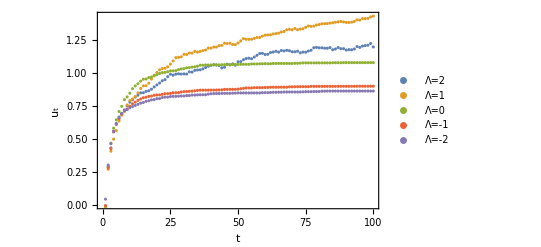

```mathematica
pΛ=ListPlot[Table[Table[Mean[rΛ⟦Λ⟧⟦3⟧⟦k⟧],{k,1,T}],{Λ,1,5}],PlotLegends->{"Λ=2","Λ=1","Λ=0","Λ=-1","Λ=-2"},IntervalMarkers->"Bands",Frame->True,FrameLabel->{Style["t",14],Style["u_t",14]}]
```

The most significant lessons from this model can be extracted from these plots. Note that if we have Λ>A_ij for all i,j, then marriage will not affect the dynamics of the system. Therefore, for sufficiently large Λ (and finite N), the system with marriage evolves the same way as the system without it. On the other hand, if Λ<A_ij for all i,j, then every agent will marry with the first matched agent they like, and the average utility will get smaller as one can see from the plots. The lesson we can extract from this result is that we should not get married to the first person we like. However, for some intermediary values of Λ∼σ, the average utility is consistently larger in the system with marriage. Therefore, it is reasonable to conclude that we should marry if we like our partner more than a sigma above average. For Λ∼σ, the lines cross, therefore, there will be a different value Λ_t that maximizes the average utility at different steps t. 
	To help further clarify the possible interpretations of the results, consider the following scenario. During our lives, we can take all opportunities we have to match others, pursuing the dream of finding the greatest love of our lives. Alternatively, after finding someone who makes us happy more than a certain amount, we can decide to stop this search. From the results of this model we may conclude that, on average, it is better to stick with someone good enough than always be looking for the big love of our lives. The conjunction of these results justifies the sentence we advertised before: don’t marry the first person you like and don’t search for the love of your life, but get married if you like your partner more than a sigma above average.
	It is also interesting to plot the evolution of u_t with the variance as we did previously for the model with and without marriage. We have

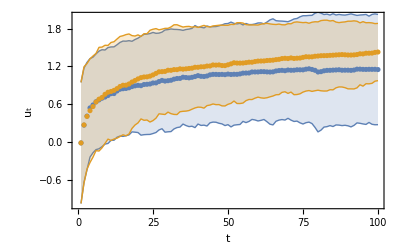

```mathematica
ListPlot[{Table[Around[Mean[rΛ⟦2⟧⟦2⟧⟦k⟧],Variance[rΛ⟦2⟧⟦2⟧⟦k⟧]],{k,1,T}],Table[Around[Mean[rΛ⟦2⟧⟦3⟧⟦k⟧],Variance[rΛ⟦2⟧⟦3⟧⟦k⟧]],{k,1,T}]},IntervalMarkers->"Bands",Frame->True,FrameLabel->{Style["t",14],Style["u_t",14]},PlotRange->{All,{-1,2}}]
```

with the orange line the average utility in the system with marriage and Λ=1 and the blue line the system without marriage. The Uniform model gives a similar result:

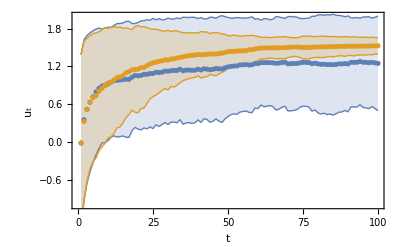

```mathematica
ListPlot[{Table[Around[Mean[rU⟦2⟧⟦k⟧],Variance[rU⟦2⟧⟦k⟧]],{k,1,T}],Table[Around[Mean[rU⟦3⟧⟦k⟧],Variance[rU⟦3⟧⟦k⟧]],{k,1,T}]},IntervalMarkers->"Bands",Frame->True,FrameLabel->{Style["t",14],Style["u_t",14]},PlotRange->{All,{-1,2}}]
```

### 2.3. Discussion, comments and empirical comparison

#### 2.3.1 Men and women

A possible point of concern, is the fact that we did not distinguished man and woman in our model. To make explicit such a distinction, however, is not important for our conclusions. We can partition society into two, making matching just between agents not of the same group. For this situation, the matching is a random surjective function from the smallest partition to the largest one. A random subset of agents that make the large partition is left out from the matching process at each step. A slightly modification of our original implementation is sufficient for that and gives similar results.

#### 2.3.2 Generalizing to μ_s≠μ and σ_s≠σ

So far we presented results in the case where all elements of the affinity matrix are generated by the same Gaussian distribution, that is μ=μ_s and σ=σ_s. So, one might rightly worry that our results are not valid if this is not the case. To address this concern, we vary the distribution of the off-diagonal elements keeping the diagonal elements fixed at A_kk=0. Using

```mathematica
{n=1000,σ=1,μs=0,σs=0.00001,Λ=1,T=100};
```

(for simplicity we used the Gaussian model for μ_s=0, σ_s=0.00001, which is approximately A_kk=0) we run the simulation

```mathematica
rμ=Table[DatingMarriageModel["N",n,μ,σ,μs,σs,μ+σ,T],{μ,{2,1,0,-1,-2}}];
```

which gives:

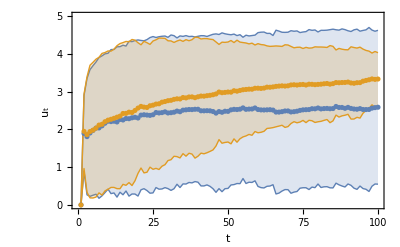
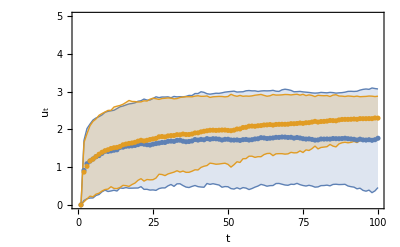
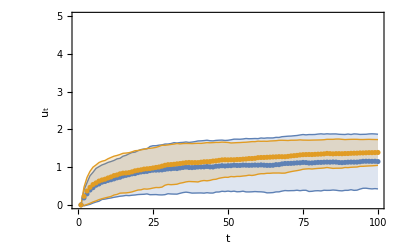
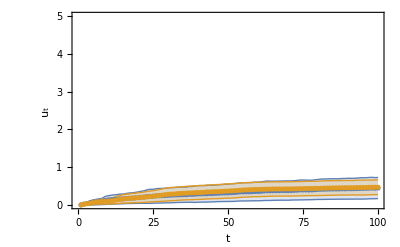
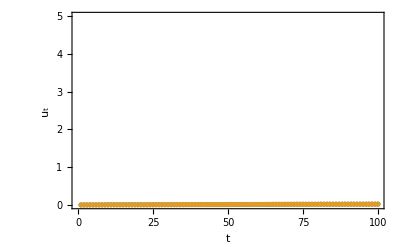
{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5}}

```mathematica
Table[{ListPlot[{Table[Around[Mean[rμ⟦μ⟧⟦2⟧⟦k⟧],Variance[rμ⟦μ⟧⟦2⟧⟦k⟧]],{k,1,T}],Table[Around[Mean[rμ⟦μ⟧⟦3⟧⟦k⟧],Variance[rμ⟦μ⟧⟦3⟧⟦k⟧]],{k,1,T}]},IntervalMarkers->"Bands",Frame->True,FrameLabel->{Style["t",14],Style["u_t",14]},PlotRange->{All,{0,5}}],μ},{μ,1,5}]
```

The following considerations are helpful to interpolate the plots above and get a better picture of the system as a function of μ. For values of μ less than -2σ=-2, an agent is unlikely to find one it likes more than being single, and the behavior of the system will be very similar to that of the last figure above. On the other extreme, if μ>2σ=2$, agents will prefer to date any other agent than being single as they did for μ=2σ=2, and the dynamics will be very similar to that of the first figure above. The difference, in this case, will be that the average utility will range on a different scale set by μ. Because for all values we have the average utility in the system with marriage higher than in the system without it, we are confident in concluding that this is a robust feature of our model. Therefore, the advice we extracted seems to hold in more general contexts.

#### 2.3.3. Homogeneity

Another objection to the results presented in the previous section is that the assumption of a homogeneous society is clearly false. What is interesting, however, is that for a finite number of agents, this homogeneity is already broken. More precisely, for all agents k, its affinity with the other agents is given by {A_jk:1≤j≤n & j≠k}, which is generated by the same distribution but is, in general, a different collection of numbers for each agent. To make this point more clear consider the following. We run a simulation

```mathematica
r=DatingMarriageModel["N",10000,μ,σ,μs,σs,Λ,T];
```

We can select all agents k such that the average of the collection {A_jk:1≤j≤n & j≠k} is larger than a certain positive value. We can pick this value in a way that we have just 5 percent of all agents selected

```mathematica
Liked=Reverse[SortBy[Table[{k,Mean[r⟦1⟧⟦k⟧]},{k,1,Length[r⟦1⟧]}],Last]]⟦1;;5 n/100⟧
```

{{1011,0.0435966},{6870,0.0387058},{528,0.0320942},{6718,0.0320186},{2248,0.0317846},{5814,0.0315959},{9393,0.0313931},{7925,0.0308366},{3760,0.0302984},{4982,0.0298786},{2705,0.029849},{9269,0.0294921},{6160,0.028845},{8115,0.0285627},{2531,0.0285157},{8285,0.0284942},{9370,0.0283262},{9028,0.02782},{9098,0.0277385},{4134,0.0276847},{9251,0.0273388},{210,0.0272683},{2859,0.0271581},{9508,0.0271551},{5776,0.0270454},{4620,0.0269798},{3415,0.0269202},{907,0.0268464},{489,0.0265831},{6345,0.0261772},{2516,0.026103},{6338,0.026045},{9761,0.0259357},{786,0.0257796},{3858,0.0256106},{6441,0.0255208},{1915,0.0254364},{6567,0.025349},{7471,0.0252955},{9556,0.0252802},{3091,0.0252211},{3590,0.0252196},{4965,0.025184},{4125,0.0251278},{8558,0.0250868},{8840,0.0250791},{1120,0.0249757},{8474,0.0248552},{7108,0.0247377},{9093,0.0246251}}

This will represent the 1 percent most liked agents of the system. Conversely, we can do the same and get the 5 percent less liked agents.

```mathematica
Disliked=SortBy[Table[{k,Mean[r⟦1⟧⟦k⟧]},{k,1,Length[r⟦1⟧]}],Last]⟦1;;5 n/100⟧
```

{{5445,-0.037072},{2542,-0.0345541},{5225,-0.0333246},{6413,-0.0324562},{141,-0.0319334},{6526,-0.0317789},{6194,-0.0317252},{631,-0.0314642},{2300,-0.030986},{6028,-0.0308484},{3546,-0.0306796},{7151,-0.0306195},{1013,-0.0304609},{974,-0.0304309},{463,-0.0300025},{8973,-0.0298803},{294,-0.0296858},{7632,-0.0295572},{5090,-0.0292207},{6692,-0.0291865},{9383,-0.0290642},{5988,-0.0290052},{3916,-0.0288272},{7444,-0.028753},{3989,-0.0286817},{729,-0.0279454},{1049,-0.0276839},{3747,-0.0276571},{6023,-0.0275097},{5512,-0.0271746},{4213,-0.0270173},{6323,-0.0268493},{5376,-0.0267845},{8138,-0.0265116},{8404,-0.0264636},{104,-0.0263979},{2982,-0.0263976},{8553,-0.0263863},{7608,-0.0263623},{9201,-0.0261504},{4238,-0.0259972},{4114,-0.0259499},{6186,-0.0258265},{3073,-0.025771},{8067,-0.0256025},{5866,-0.0255041},{5436,-0.0253689},{4518,-0.0252261},{5016,-0.0252062},{2846,-0.0251686}}

It is then interesting to follow the evolution of average utility for these different sets of agents.

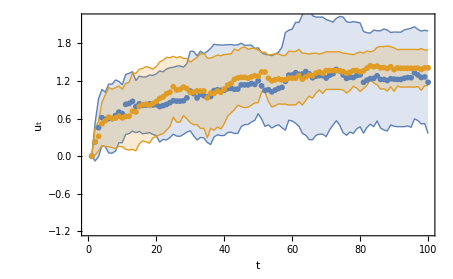
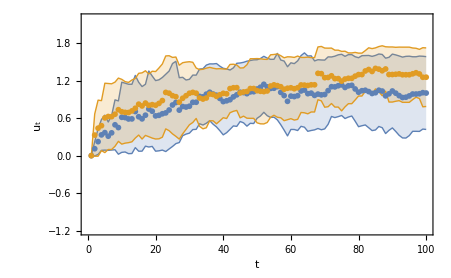

```mathematica
{ListPlot[{Table[Around[Mean[Table[r⟦2⟧⟦t⟧⟦k⟧,{k,Likedᵀ⟦1⟧}]],Variance[Table[r⟦2⟧⟦t⟧⟦k⟧,{k,Likedᵀ⟦1⟧}]]],{t,1,100}],Table[Around[Mean[Table[r⟦3⟧⟦t⟧⟦k⟧,{k,Likedᵀ⟦1⟧}]],Variance[Table[r⟦3⟧⟦t⟧⟦k⟧,{k,Likedᵀ⟦1⟧}]]],{t,1,100}]},IntervalMarkers->"Bands",Frame->True,FrameLabel->{{Style["u_t",16],None},{Style["t",16],Style["Most liked",20]}},PlotRange->{All,{-1.2,2.2}}],ListPlot[{Table[Around[Mean[Table[r⟦2⟧⟦t⟧⟦k⟧,{k,Dislikedᵀ⟦1⟧}]],Variance[Table[r⟦2⟧⟦t⟧⟦k⟧,{k,Dislikedᵀ⟦1⟧}]]],{t,1,100}],Table[Around[Mean[Table[r⟦3⟧⟦t⟧⟦k⟧,{k,Dislikedᵀ⟦1⟧}]],Variance[Table[r⟦3⟧⟦t⟧⟦k⟧,{k,Dislikedᵀ⟦1⟧}]]],{t,1,100}]},IntervalMarkers->"Bands",Frame->True,FrameLabel->{{Style["u_t",16],None},{Style["t",16],Style["Most disliked",20]}},PlotRange->{All,{-1.2,2.2}}]}
```

One finds that marriage is more beneficial to those that are not that liked. This agrees with intuition. If everyone likes you, you should not be concerned with marriage as a search strategy. It is easier for you to find a nice partner that also likes you and your mate is less likely to leave you because of someone else.

#### 2.3.4. Empirical comparison

It is hard to measure the average utility in a real societies, but the number of married couples is not. By comparing the share of married couples in our model and reality we can test the adequacy of our model to describe reality. First, we download data from https://ourworldindata.org/marriages-and-divorces:

```mathematica
data={{"Year of birth","Age","Share of men that are married"},{1900,17,0},{1900,18,0},{1900,19,1},{1900,20,2},{1900,21,6},{1900,22,14},{1900,23,21},{1900,24,30},{1900,25,40},{1900,26,48},{1900,27,56},{1900,28,63},{1900,29,68},{1900,30,73},{1900,31,77},{1900,32,79},{1900,33,82},{1900,34,83},{1900,35,85},{1900,36,86},{1900,37,87.1},{1900,38,88.1},{1900,39,88.8},{1900,40,89.6},{1900,41,90.2},{1900,42,90.7},{1900,43,91.1},{1900,44,91.5},{1900,45,91.8},{1900,46,92.1},{1900,47,92.3},{1900,48,92.5},{1900,49,92.7},{1900,50,92.9},{1910,17,0},{1910,18,0},{1910,19,0},{1910,20,2},{1910,21,4},{1910,22,9},{1910,23,15},{1910,24,23},{1910,25,32},{1910,26,41},{1910,27,50},{1910,28,58},{1910,29,64},{1910,30,70},{1910,31,75},{1910,32,78},{1910,33,80},{1910,34,82},{1910,35,83},{1910,36,84},{1910,37,85.7},{1910,38,86.8},{1910,39,87.7},{1910,40,88.3},{1910,41,88.9},{1910,42,89.4},{1910,43,89.8},{1910,44,90.1},{1910,45,90.4},{1910,46,90.6},{1910,47,90.8},{1910,48,91},{1910,49,91.2},{1910,50,91.3},{1920,17,0},{1920,18,0},{1920,19,1},{1920,20,2},{1920,21,7},{1920,22,17},{1920,23,27},{1920,24,34},{1920,25,42},{1920,26,51},{1920,27,59},{1920,28,66},{1920,29,72},{1920,30,76},{1920,31,80},{1920,32,82},{1920,33,84},{1920,34,86},{1920,35,87},{1920,36,88},{1920,37,88.4},{1920,38,89},{1920,39,89.5},{1920,40,89.9},{1920,41,90.3},{1920,42,90.6},{1920,43,90.8},{1920,44,91.1},{1920,45,91.3},{1920,46,91.4},{1920,47,91.6},{1920,48,91.7},{1920,49,91.8},{1920,50,91.9},{1930,17,0},{1930,18,0},{1930,19,1},{1930,20,3},{1930,21,7},{1930,22,17},{1930,23,28},{1930,24,40},{1930,25,51},{1930,26,61},{1930,27,68},{1930,28,73},{1930,29,77},{1930,30,81},{1930,31,83},{1930,32,85},{1930,33,86},{1930,34,87},{1930,35,88},{1930,36,89},{1930,37,89.1},{1930,38,89.5},{1930,39,89.9},{1930,40,90.3},{1930,41,90.5},{1930,42,90.8},{1930,43,91},{1930,44,91.3},{1930,45,91.4},{1930,46,91.6},{1930,47,91.7},{1930,48,91.8},{1930,49,91.9},{1930,50,92},{1940,17,0},{1940,18,0},{1940,19,2},{1940,20,6},{1940,21,14},{1940,22,26},{1940,23,38},{1940,24,50},{1940,25,60},{1940,26,68},{1940,27,74},{1940,28,78},{1940,29,81},{1940,30,83},{1940,31,85},{1940,32,87},{1940,33,88},{1940,34,89},{1940,35,89},{1940,36,90},{1940,37,90.1},{1940,38,90.5},{1940,39,90.8},{1940,40,91.1},{1940,41,91.4},{1940,42,91.6},{1940,43,91.7},{1940,44,91.8},{1940,45,92},{1940,46,92.1},{1940,47,92.2},{1940,48,92.3},{1940,49,92.3},{1940,50,92.4},{1950,17,0},{1950,18,1},{1950,19,4},{1950,20,9},{1950,21,18},{1950,22,30},{1950,23,42},{1950,24,52},{1950,25,60},{1950,26,66},{1950,27,70},{1950,28,74},{1950,29,77},{1950,30,79},{1950,31,81},{1950,32,82},{1950,33,83},{1950,34,84},{1950,35,85},{1950,36,86},{1950,37,86.5},{1950,38,87},{1950,39,87.4},{1950,40,87.8},{1950,41,88.1},{1950,42,88.3},{1950,43,88.6},{1950,44,88.8},{1950,45,88.9},{1950,46,89.1},{1950,47,89.2},{1950,48,89.3},{1950,49,89.4},{1950,50,89.5},{1960,17,0},{1960,18,1},{1960,19,3},{1960,20,6},{1960,21,12},{1960,22,19},{1960,23,26},{1960,24,34},{1960,25,41},{1960,26,47},{1960,27,52},{1960,28,57},{1960,29,61},{1960,30,64},{1960,31,67},{1960,32,69},{1960,33,71},{1960,34,72},{1960,35,74},{1960,36,75},{1960,37,75.8},{1960,38,76.6},{1960,39,77.4},{1960,40,78},{1960,41,78.6},{1960,42,79.1},{1960,43,79.5},{1960,44,79.9},{1960,45,80.3},{1960,46,80.6},{1960,47,80.9},{1960,48,81.1},{1960,49,81.3},{1960,50,81.5},{1970,17,0},{1970,18,0},{1970,19,1},{1970,20,2},{1970,21,4},{1970,22,7},{1970,23,11},{1970,24,15},{1970,25,19},{1970,26,24},{1970,27,29},{1970,28,33},{1970,29,37},{1970,30,41},{1970,31,45},{1970,32,48},{1970,33,51},{1970,34,54},{1970,35,56},{1970,36,58},{1970,37,59.6},{1970,38,61},{1970,39,62.2},{1970,40,63.3},{1970,41,64.3},{1970,42,65.1},{1980,17,0},{1980,18,0},{1980,19,0},{1980,20,1},{1980,21,1},{1980,22,3},{1980,23,4},{1980,24,6},{1980,25,9},{1980,26,11},{1980,27,15},{1980,28,18},{1980,29,22},{1980,30,25},{1980,31,29},{1980,32,33},{1990,17,0},{1990,18,0},{1990,19,0},{1990,20,0},{1990,21,1},{1990,22,1}};
```

After organizing the data:

```mathematica
d00={Table[data⟦k⟧⟦2⟧,{k,2,35}],Table[data⟦k⟧⟦3⟧,{k,2,35}]}ᵀ;
d10={Table[data⟦k⟧⟦2⟧,{k,36,69}],Table[data⟦k⟧⟦3⟧,{k,36,69}]}ᵀ;d20={Table[data⟦k⟧⟦2⟧,{k,70,103}],Table[data⟦k⟧⟦3⟧,{k,70,103}]}ᵀ;
d30={Table[data⟦k⟧⟦2⟧,{k,104,137}],Table[data⟦k⟧⟦3⟧,{k,104,137}]}ᵀ;
d40={Table[data⟦k⟧⟦2⟧,{k,138,171}],Table[data⟦k⟧⟦3⟧,{k,138,171}]}ᵀ;
d50={Table[data⟦k⟧⟦2⟧,{k,172,205}],Table[data⟦k⟧⟦3⟧,{k,172,205}]}ᵀ;
d60={Table[data⟦k⟧⟦2⟧,{k,206,239}],Table[data⟦k⟧⟦3⟧,{k,206,239}]}ᵀ;
d70={Table[data⟦k⟧⟦2⟧,{k,240,265}],Table[data⟦k⟧⟦3⟧,{k,240,265}]}ᵀ;
d80={Table[data⟦k⟧⟦2⟧,{k,265,281}],Table[data⟦k⟧⟦3⟧,{k,265,281}]}ᵀ;
d90={Table[data⟦k⟧⟦2⟧,{k,282,287}],Table[data⟦k⟧⟦3⟧,{k,282,287}]}ᵀ;
```

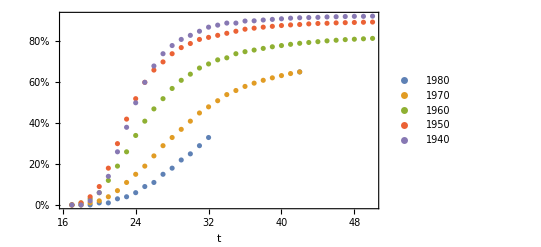

```mathematica
pdata=ListPlot[{d80,d70,d60,d50,d40},Frame->True,FrameTicks->{{{{0,"0%"},{10,"10%"},{20,"20%"},{30,"30%"},{40,"40%"},{50,"50%"},{60,"60%"},{70,"70%"},{80,"80%"},{90,"90%"}},None},{Automatic,None}},FrameLabel->{Style["t",14]},PlotLegends->{"1980","1970","1960","1950","1940"}]
```

We can compare this values with what we obtain in our simulation:

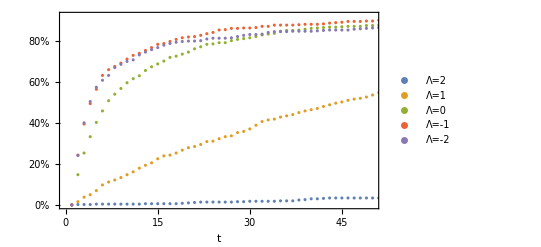
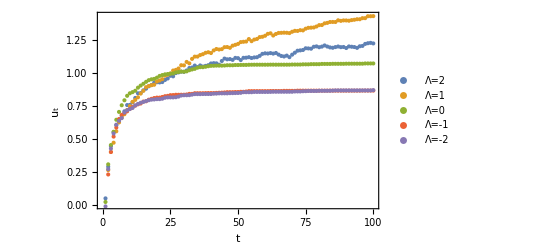
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
MarriageCouplesΛ=Table[Table[Length[Select[rΛ⟦Λ⟧⟦5⟧⟦k⟧,MemberQ[rΛ⟦Λ⟧⟦6⟧,#]&]],{k,1,T}],{Λ,1,5}];
psimulation=ListPlot[(2MarriageCouplesΛ)/n,PlotLegends->{"Λ=2","Λ=1","Λ=0","Λ=-1","Λ=-2"},PlotRange->{{0,50},All},Frame->True,FrameTicks->{{{{0.0,"0%"},{0.1,"10%"},{0.2,"20%"},{0.3,"30%"},{0.4,"40%"},{0.5,"50%"},{0.6,"60%"},{0.7,"70%"},{0.8,"80%"},{0.9,"90%"}},None},{Automatic,None}},FrameLabel->{Style["t",14]}];
{pdata,psimulation,pΛ}
```

The trends of a declining number of married men in the data from Our World in Data can be interpreted in the framework of our model as a shift to higher Λ. This agrees with rough expectations. In the past, marriage was enforced by tradition and many couples get married without high affinity. Progressive movements diminished the forces of tradition and people became more rigorous to get married. If we go further and assume that each generation is associated with a value of Λ with the same color in the plot from our model, we can see from the plots with the evolution of average utility that the average utility concerning relationships increased from 1940 to 1970, and perhaps starts decreasing from 1970 to 1980. This being true, would suggest that the progressive movements benefited the matching markets of traditional societies by increasing Λ. But perhaps, Λ went too high and needs to be balanced. The right balance can be achieved following the piece of advice extracted from the results of the previous section: get married if you like your partner more than a sigma above average. The steps t are likely not linearly related to chronological time. If initial steps are compressed, as it is reasonable to assume, the initial convex behavior of the real-world data may be attained.

## 3. Analytical formulation in the large N limit

For this last section we will simply wrote the analytical evolution equations for our system in the large N limit for the Uniform model. An proper explanation and derivation of the results can be found in the aforementioned paper: https://arxiv.org/pdf/2108.04885.pdf

### 3.1. Evolution equations for the Uniform model

Here we define a function that gives b_(t+1),r_(t+1)p_(c(t+1))p_(s(t+1)) given b_t,r_t,p_ct,p_st for the Uniform model with pA=p0=NormalDistribution:

```mathematica
Clear[σ]
NextStep[p_,ps_,pc_,b_,r_]:=Module[{pA,ExV,fc,cn,cn1,Cn,fs,sn,sn1,Sn,n,k,l,m,ml,bNext,pcNext,rNext,psNext},
pA=1/(4σ);
ExV[exp_,dist_]:=(Integrate[exp dist,u]/.{u->2σ})-(Integrate[exp dist,u]/.{u->-2σ});


(*If in a couple*)
fc=k^n Integrate[pA,{u,ml,2σ}]Integrate[pA,{u,-2σ,m}]+k^n Integrate[pA,{u,-2σ,ml}];
cn=Integrate[pA,{u,l,2σ}](pA ((2σ)^(n+1)-k^(n+1))/(n+1)+fc  Integrate[pA,{u,-2σ,k}])+fc Integrate[pA,{u,-2σ,l}];
cn1=pA ((2σ)^(n+1)-k^(n+1))/(n+1)Integrate[pA,{u,l,2σ}];
Cn=b ExV[ExV[ExV[ExV[cn/.{k->u},pc]/.{l->u},p]/.{m->u},pc]/.{ml->u},p]+r ExV[ExV[cn1/.{k->u},ps]/.{l->u},p];


(*If single*)
fs=pA((2σ)^(n+1)-(-2σ)^(n+1))/(n+1)Integrate[pA,{u,m,2σ}]Integrate[pA,{u,ml,2σ}];
sn=fs Integrate[pA,{u,l,2σ}]Integrate[pA,{u,-2σ,k}]+fs Integrate[pA,{u,-2σ,l}];
sn1=k^n Integrate[pA,{u,-2σ,k}]Integrate[pA,{u,l,2σ}]+k^n Integrate[pA,{u,-2σ,l}];
Sn=b ExV[ExV[ExV[ExV[sn/.{k->u},pc]/.{l->u},p]/.{m->u},pc]/.{ml->u},p]+r ExV[ExV[sn1/.{k->u},ps]/.{l->u},p];

(*Built fractions and distributions*)
bNext=Cn/.{n->0};
rNext=Sn/.{n->0};
pcNext=FullSimplify[1/bNext √(1/(2π))InverseFourierTransform[Sum[Cn (ⅈ k)^n/(n!),{n,0,∞}],k,u]];
psNext=FullSimplify[1/rNext √(1/(2π))InverseFourierTransform[Sum[Sn (ⅈ k)^n/(n!),{n,0,∞}],k,u]];
{bNext,rNext,pcNext,psNext}]
```

#### 3.1.1. Step 1

Using the NextStep function we can compute the fractions and distributions b_1,r_1 p_c1 p_s1, they are simply

```mathematica
{b1,r1,pc1,ps1}=Simplify[NextStep[1/(4σ),1/(4σ),0,0,1],Assumptions->-2σ<u<2σ]
```

{1/4,3/4,(u+2 σ)/(8 σ^2),(u+6 σ)/(24 σ^2)}

We can then compare the results with what we obtained with the simulations:

```mathematica
rU=DatingMarriageModel["U",10000,0,1,0,1,1,1];
```

By split the couples and singles we can make the histogram with the utility distribution at t=1 for singles and couples and compare the results with the analytical distributions obtained

```mathematica
CouplesUtility=Table[rU⟦2⟧⟦2⟧⟦n⟧,{n,Flatten[rU⟦4⟧⟦2⟧]}];
SinglesUtility=Table[rU⟦2⟧⟦2⟧⟦n⟧,{n,Complement[Table[n,{n,1,10000}],Flatten[rU⟦4⟧⟦2⟧]]}];
```

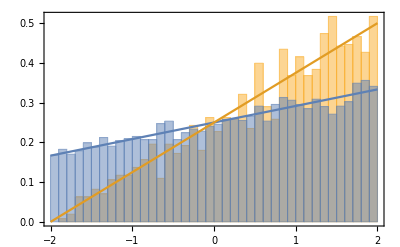

```mathematica
Show[Histogram[{CouplesUtility,SinglesUtility},50,"PDF"],Plot[{ps1/.{σ->1},pc1/.{σ->1}},{u,-2,2}],Frame->True]
```

Conversely, we can plot the distributions at t=0,1 and compare them with the histograms obtained from the simulation:

```mathematica
p0=1/(4σ);
p1=Simplify[b1 pc1+r1 ps1]
```

(u+4 σ)/(16 σ^2)

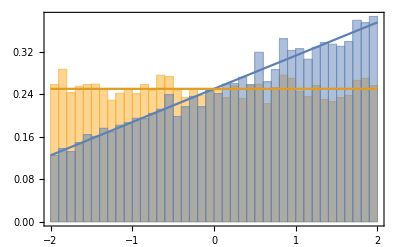

```mathematica
Show[Histogram[rU⟦2⟧,50,"PDF"],Plot[{p1/.{σ->1},p0/.{σ->1}},{u,-2,2}],Frame->True]
```

#### 3.1.2. Step 2

Using the results for step 1 we can using NextStep again to find the results for step 2:

```mathematica
{b2,r2,pc2,ps2}=Simplify[NextStep[p1,ps1,pc1,b1,r1],Assumptions->-2σ<u<2σ]
```

{1861/5184,3323/5184,(3 (u+2 σ) (335 u+2258 σ))/(59552 σ^3),(135 u^2+1836 u σ+6466 σ^2)/(26584 σ^3)}

Again, we can compare the results obtained with data. We have:

```mathematica
rU=DatingMarriageModel["U",10000,0,1,0,1,1,2];
```

```mathematica
p={1/(4σ),Simplify[b1 pc1+r1 ps1],Simplify[b2 pc2+r2 ps2]}
```

{1/(4 σ),(u+4 σ)/(16 σ^2),(1545 u^2+16128 u σ+39412 σ^2)/(165888 σ^3)}

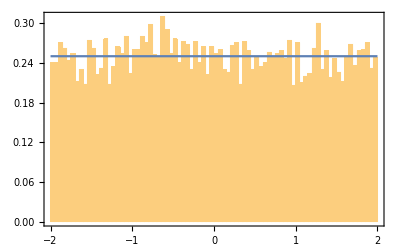
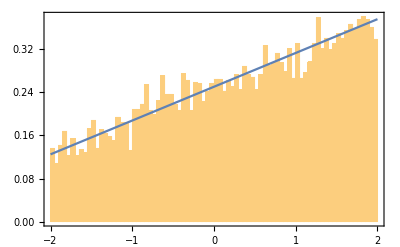
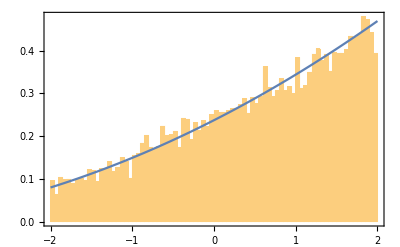

```mathematica
Table[Show[Histogram[rU⟦3⟧⟦k⟧,100,"PDF"],Plot[p⟦k⟧/.{σ->1},{u,-2,2}],Frame->True],{k,1,3}]
```

#### 3.1.3. Steps: 3, 4, and 5

```mathematica
{b3,r3,pc3,ps3}=Simplify[NextStep[b2 pc2+r2 ps2,ps2,pc2,b2,r2],Assumptions->-2σ<u<2σ]
```

{738520201/1758243024,1019722823/1758243024,(3 (u+2 σ) (117837025 u^2+1750052390 u σ+6553731184 σ^2))/(189061171456 σ^4),(33916725 u^3+759734640 u^2 σ+5683639158 u σ^2+15302585648 σ^3)/(65262260672 σ^4)}

```mathematica
{b4,r4,pc4,ps4}=Simplify[NextStep[b3 pc3+r3 ps3,ps3,pc3,b3,r3],Assumptions->-2σ<u<2σ]
```

{31955539567148529492880580987321681/69612382462607773764270992312500224,37656842895459244271390411325178543/69612382462607773764270992312500224,((u+2 σ) (60214282127945002445911460191439125 u^3+1447583090151863810099298770901342900 u^2 σ+11594976776947968756945045371570339700 u σ^2+31657941122785317967430679347680578976 σ^3))/(331315034232195953782185863676551188608 σ^5),(7130257703062469949940297992000 u^4+229384222881536614221585648086400 u^3 σ+2755390664975140756359321807139200 u^2 σ^2+14891483311097097429186410728118528 u σ^3+33960171850842590025738173295418543 σ^4)/(150627371581836977085561645300714172 σ^5)}

```mathematica
Clear[σ]
{b5,r5,pc5,ps5}=Simplify[NextStep[b4 pc4+r4 ps4,ps4,pc4,b4,r4],Assumptions->-2σ<u<2σ]
```

{73099181565308899938080196329737180436831187812881420670193656158565028673053204696561492252520748921877033832638269235868337368934714003700726852049/150345603785271930997778710458418265301329076783777720002087073069581925788102823765021433690775405193649083599065269763238291515323334009953636581376,77246422219963031059698514128681084864497888970896299331893416911016897115049619068459941438254656271772049766427000527369954146388620006252909729327/150345603785271930997778710458418265301329076783777720002087073069581925788102823765021433690775405193649083599065269763238291515323334009953636581376,(3 (u+2 σ) (200247489355726037766455399500062947250046527231091638804420392762157323767518816893488400402168826812149315901114878924483685554149835188878275625 u^4+6832890677909980385303964552040837062839465342917743077699656639760753071317590364556003309073541719400196153349589568287137128554495997728757555250 u^3 σ+87143084218766579841507358689187399443860492548506639947052285634932340555025345195572153027247245673665742642713674840079080672188638278600879210300 u^2 σ^2+496514386405257968937911351504793892353691383118275833680290529071965482964472588349938516302526568736909496180650903982271754500309038669866845748120 u σ^3+1100675419780801487661087808550615181093047134428803016412707668607711060625288642901907851639957329947043542462654663668420152774689215525266014160832 σ^4))/(37426780961438156768297060520825436383657568160195287383139151953185294680603240804639484033290623448001041322310793848764588732894573569894772148249088 σ^6),(1223420984028526335338987245547775068995701115189640554181577185992677861881726343872974242246464683235706441147728011340726834055582937251840000 u^5+52310869470786673695045259335206873971230358094869888138967478678860151813470377761169545661239463795426047076097490832366299284494162650464256000 u^4 σ+889471536358651105062865354278071317398451856952752627518127687954259242874525595332772369182870483819954404750800139777486081491948781889493401600 u^3 σ^2+7560521111131896024990374066209519853755233484198603370956549036733101949842003761465599446315947135554250395705628126456645816025987117596656271360 u^2 σ^3+32878668395880586356183865788340622215200443916127128786484429321427329161891200263407160382912767840447879447956044588211424865187296391981183270912 u σ^4+66998332622813985670553870543862396396116307179394577861906655596933742029457175511003399630384093806887685888175984388097520900643589195642549081647 σ^5)/(308985688879852124238794056514724339457991555883585197327573667644067588460198476273839765753018625087088199065708002109479816585554480025011638917308 σ^6)}

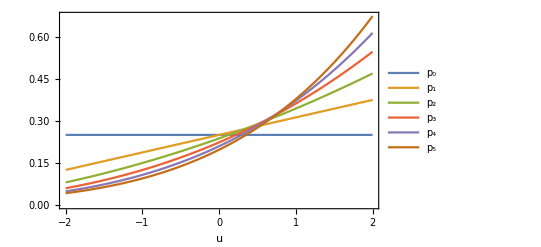

```mathematica
σ=1;
Plot[{1/4,b1 pc1+r1 ps1,b2 pc2+r2 ps2,b3 pc3+r3 ps3,b4 pc4+r4 ps4,b5 pc5+r5 ps5},{u,-2,2},PlotLegends->{"p_0","p_1","p_2","p_3","p_4","p_5"},Frame->True,FrameLabel->{"u"}]
```

### 3.2. Distribution for married couples:

In the model with marriage, married couples decouple from the system because they do not break. More precisely, they are not selected in the matching process. This sole fact, allows us to derive an expression for the utility distribution for married couples. Here we just compare the distribution we computed with the simulation:

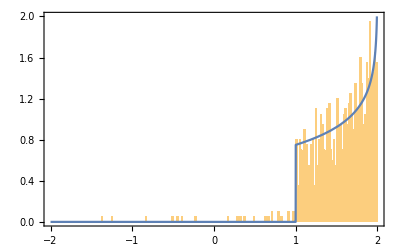

```mathematica
rU=DatingMarriageModel["U",1000,0,1,0,1,1,100];Show[Histogram[rU⟦3⟧⟦100⟧,100,"PDF"],Plot[(Log[(2σ-Λ)/(2σ-u)]HeavisideTheta[u-Λ] 1/(4σ)+1/(4σ)(Λ+2σ)/(2σ-Λ)HeavisideTheta[u-Λ])/.{σ->1,Λ->1},{u,-2,2}],Frame->True,PlotRange->{{-2,2},{0,2}}]
```